```mathematica
(*This just rewrites a whole mess of variables from a Mathematica notation to a Matlab notation*)
varreplace=Flatten@{{Nx[x,y,z]->Nx,Ny[x,y,z]->Ny,Nz[x,y,z]->Nz,Table[D[Nx[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNxd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[Ny[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNyd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[Nz[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNzd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],Table[D[Nx[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nxd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[Ny[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nyd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[Nz[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nzd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}]},{Nx[x,y]->Nx,Ny[x,y]->Ny,Table[D[Nx[x,y],{x,y}⟦ii⟧]->ToExpression["dNxd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],
Table[D[Ny[x,y],{x,y}⟦ii⟧]->ToExpression["dNyd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],Table[D[Nx[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2Nxd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}],Table[D[Ny[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2Nyd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}]},Flatten@{θ[x,y,z]->θ,ϕ[x,y,z]->ϕ,Table[D[θ[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dθd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[ϕ[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dϕd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[θ[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2θd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[ϕ[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2ϕd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}]},Flatten@{ϕ[x,y]->ϕ,
Table[D[ϕ[x,y],{x,y}⟦ii⟧]->ToExpression["dϕd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],
Table[D[ϕ[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2ϕd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}]}};
```

Director:

```mathematica
(*A few options here. Uncomment your chouce and evaluate the whole notebook. It may take a while for the 3D cases, especially with saddlesplay.*)
(*3D Cartesian:*)
(*n:={Nx[x,y,z],Ny[x,y,z],Nz[x,y,z]}
vars:={Nx[x,y,z],Ny[x,y,z],Nz[x,y,z]}
fgS := -Ws*({Wx, Wy, Wz}.n)^2*)

(*2D Cartesian*)
(*n:={Nx[x,y],Ny[x,y],0}
vars:={Nx[x,y],Ny[x,y]}*)
(*fgS=-Ws ({Bx,By,Bz}.n)^2;*)

(*3D Spherical*)
n:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}/.{θ->θ[x,y,z],ϕ->ϕ[x,y,z]}
vars:={θ[x,y,z],ϕ[x,y,z]}
fgS := -Ws*({Sin[α]Cos[β],Sin[α]Sin[β], Cos[α]}.n)^2 /. {α->α[x,y,x], β->β[x,y,x]}

(*2D Polar*)
(*n:={Cos[ϕ],Sin[ϕ],0}/.{ϕ->ϕ[x,y]}
vars:={ϕ[x,y]}
fgS:= -Ws*({Cos[α],Sin[α],0}.n)^2/.{α-> α[x,y]}*)
```

Levi-civita tensor:

```mathematica
ϵ=Normal@LeviCivitaTensor[3];
```

Equations 4 & 5. Q with 2 arguments will form the components of the Q-tensor, and Q with 3 arguments will take the derivative of an element of the Q tensor with respect to a variable.

```mathematica
Q[j_,k_]:=S/2(3 n⟦j⟧n⟦k⟧-KroneckerDelta[j,k])
Q[j_,k_,l_]:=D[Q[j,k],{x,y,z}⟦l⟧]
```

Equation 3. Einstein summation notation means that the repeated indices are summed over. For now, we will not need G_3^(2) (which contains the saddle-splay term) or G_4^(2) (which accounts for cholesteric pitch). However, we will need G_3^(2) when it comes time to encode weak boundaries!

```mathematica
G12=Sum[Q[j,k,l]Q[j,k,l],{j,3},{k,3},{l,3}]//Simplify;
G22=Sum[Q[j,k,k]Q[j,l,l],{j,3},{k,3},{l,3}]//Simplify;
G32=Sum[Q[j,k,l]Q[j,l,k],{j,3},{k,3},{l,3}]//Simplify;
G42=Sum[ϵ⟦j,k,l⟧Q[j,m]Q[k,m,l],{j,3},{k,3},{l,3},{m,3}]//Simplify;
G63=Sum[Q[j,k]Q[l,m,j]Q[l,m,k],{j,3},{k,3},{l,3},{m,3}]//Simplify;
```

Equaton 13 (we aren’t doing anything with electric fields, thankfully).

```mathematica
(*Note the K24 saddle-splay term. Multiply it by 0 if you don't want it.*)
fgQ=Collect[Simplify[1/27(K33-K11+3K22)G12/S^2+2/9(K11-K22-0*K24)G22/S^2+2/9 G32/S^2+2/27(K33-K11)G63/S^3],{K11,K22,K33},Simplify];
```

```mathematica
bend:=1/2 K11 Div[n,{x,y,z}]^2//FullSimplify
twist:=1/2 K22(n.Curl[n,{x,y,z}])^2//FullSimplify
splay:=1/2 K33(Cross[n,Curl[n,{x,y,z}]].Cross[n,Curl[n,{x,y,z}]])//Simplify
(*Del={D[#,x],D[#,y],D[#,z]}&;
saddlesplay:=1/2 K24 Div[(n.Del[#]&)@n-n(Div[n,{x,y,z}]),{x,y,z}]//FullSimplify*)
saddlesplay=0;
(*Comment the saddle-splay back in if you choose.*)
fgOF=bend+twist+splay+saddlesplay;
```

```mathematica
(*Pick which form of the free energy to use, including the surface energy if you so choose (scaled by factor Ws). The surface energy applies an energy bonus for aligned with the preferred direction notated by the unit vector {Bx,By,Bz}. Feel free to define this in spherical coordinates or whatever.*)
(*fgS=-Ws ({Bx,By,Bz}.n)^2;*)



(*use this line to switch between Oseen Frank and Q tensor representations*)
fg=fgOF + fgS;
(*fg = fgQ;*)
```

```mathematica
(*1/2 K33 (Sin[ϕ[x,y]] ϕ^(0,1)[x,y]+Cos[ϕ[x,y]] ϕ^(1,0)[x,y])^2+1/2 K11 (Cos[ϕ[x,y]] ϕ^(0,1)[x,y]-Sin[ϕ[x,y]] ϕ^(1,0)[x,y])^2/.varreplace//ToMatlab*)
```

```mathematica
fg /.varreplace
```

1/2 K11 (-dθdz Sin[θ]+Cos[ϕ] (dθdx Cos[θ]+dϕdy Sin[θ])+(dθdy Cos[θ]-dϕdx Sin[θ]) Sin[ϕ])^2+1/8 K22 (-2 dϕdz Sin[θ]^2+Cos[ϕ] (-2 dθdy+dϕdx Sin[2 θ])+(2 dθdx+dϕdy Sin[2 θ]) Sin[ϕ])^2+1/32 K33 (16 Sin[θ]^2 (dθdz Cos[θ]+Sin[θ] (dθdx Cos[ϕ]+dθdy Sin[ϕ]))^2+(4 dϕdx Cos[ϕ]^2 Sin[θ]^2+2 dθdy Sin[2 θ]+2 dϕdz Cos[ϕ] Sin[2 θ]-2 dθdy Cos[ϕ]^2 Sin[2 θ]+4 dθdz Cos[θ]^2 Sin[ϕ]+2 dϕdy Sin[θ]^2 Sin[2 ϕ]+dθdx Sin[2 θ] Sin[2 ϕ])^2+(4 dθdz Cos[θ]^2 Cos[ϕ]+2 dθdx Sin[2 θ]-2 dϕdz Sin[2 θ] Sin[ϕ]-4 dϕdy Sin[θ]^2 Sin[ϕ]^2-2 dθdx Sin[2 θ] Sin[ϕ]^2-2 dϕdx Sin[θ]^2 Sin[2 ϕ]+dθdy Sin[2 θ] Sin[2 ϕ])^2)-Ws (Cos[θ] Cos[α[x,y,x]]+Cos[ϕ] Cos[β[x,y,x]] Sin[θ] Sin[α[x,y,x]]+Sin[θ] Sin[ϕ] Sin[α[x,y,x]] Sin[β[x,y,x]])^2

```mathematica
(*General form for Euler-Lagrange equations. Notice the intermittent Simplify's. This is a little quicker than doing it all at the end.*)
ELeqs=Flatten@Table[
D[fg,vars⟦ELii⟧]-Sum[Simplify@D[Simplify@Quiet@D[fg,Simplify@D[vars⟦ELii⟧,{x,y,z}⟦ii⟧]],{x,y,z}⟦ii⟧],{ii,3}],{ELii,Length@vars}];
```

```mathematica
(*Download this package online.*)
<<ToMatlab`
```

```mathematica
(*You now have an array that has the Euler-Lagrange equation for each of your variables. Replace the number to view the EL equation for the corresponding variable.*)
vars
```

{θ[x,y,z],ϕ[x,y,z]}

```mathematica
(*Check out the one constant approximation to see if it makes sense.*)
(*ELeqs/.{K11->5*^-12,K22->5*^-12,K33->5*^-12} ;*)
```

```mathematica
ELeqsSimp=Collect[#,{K11,K22,K33,K24},FullSimplify]&/@ELeqs
```

```mathematica
ELeqs⟦1⟧ /. varreplace //ToMatlab
```

K11.*((-1).*dθdz.*cos(θ)+cos(ϕ).*(dϕdy.*cos(θ)+(-1).*dθdx.*sin(θ)) ...
  +((-1).*dϕdx.*cos(θ)+(-1).*dθdy.*sin(θ)).*sin(ϕ)).*((-1).*dθdz.* ...
  sin(θ)+cos(ϕ).*(dθdx.*cos(θ)+dϕdy.*sin(θ))+(dθdy.*cos(θ)+(-1).* ...
  dϕdx.*sin(θ)).*sin(ϕ))+(1/2).*((-1).*d2θdzdz.*(K11+K33+((-1).*K11+ ...
  K33).*cos(2.*θ))+d2ϕdydz.*K11.*cos(ϕ)+(-1).*dϕdx.*dϕdz.*K11.*cos( ...
  ϕ)+(-1).*d2ϕdydz.*K11.*cos(θ).^2.*cos(ϕ)+dϕdx.*dϕdz.*K11.*cos(θ) ...
  .^2.*cos(ϕ)+2.*dθdx.*dθdz.*K11.*cos(2.*θ).*cos(ϕ)+(-2).*dθdx.* ...
  dθdz.*K33.*cos(2.*θ).*cos(ϕ)+d2ϕdydz.*K11.*cos(ϕ).*sin(θ).^2+(-1) ...
  .*dϕdx.*dϕdz.*K11.*cos(ϕ).*sin(θ).^2+(-2).*dθdz.^2.*(K11+(-1).* ...
  K33).*sin(2.*θ)+d2θdxdz.*K11.*cos(ϕ).*sin(2.*θ)+2.*dθdz.*dϕdy.* ...
  K11.*cos(ϕ).*sin(2.*θ)+dθdy.*dϕdz.*(K11+(-1).*K33).*cos(ϕ).*sin( ...
  2.*θ)+(-1).*d2θdxdz.*K33.*cos(ϕ).*sin(2.*θ)+(-1).*d2ϕdxdz.*K11.* ...
  sin(ϕ)+(-1).*dϕdy.*dϕdz.*K11.*sin(ϕ)+d2ϕdxdz.*K11.*cos(θ).^2.*sin( ...
  ϕ)+dϕdy.*dϕdz.*K11.*cos(θ).^2.*sin(ϕ)+2.*dθdy.*dθdz.*(K11+(-1).* ...
  K33).*cos(2.*θ).*sin(ϕ)+(-1).*d2ϕdxdz.*K11.*sin(θ).^2.*sin(ϕ)+(-1) ...
  .*dϕdy.*dϕdz.*K11.*sin(θ).^2.*sin(ϕ)+(-2).*dθdz.*dϕdx.*K11.*sin( ...
  2.*θ).*sin(ϕ)+(-1).*dθdx.*dϕdz.*K11.*sin(2.*θ).*sin(ϕ)+d2θdydz.*( ...
  K11+(-1).*K33).*sin(2.*θ).*sin(ϕ)+dθdx.*dϕdz.*K33.*sin(2.*θ).*sin( ...
  ϕ))+(1/4).*K22.*(2.*dϕdx.*cos(2.*θ).*cos(ϕ)+(-4).*dϕdz.*cos(θ).* ...
  sin(θ)+2.*dϕdy.*cos(2.*θ).*sin(ϕ)).*((-2).*dϕdz.*sin(θ).^2+cos(ϕ) ...
  .*((-2).*dθdy+dϕdx.*sin(2.*θ))+(2.*dθdx+dϕdy.*sin(2.*θ)).*sin(ϕ))+ ...
  (1/4).*(4.*dθdy.*dϕdx.*K22.*cos(ϕ).^2+(-4).*d2θdxdx.*K11.*cos(θ) ...
  .^2.*cos(ϕ).^2+(-4).*dθdy.*dϕdx.*K11.*cos(θ).^2.*cos(ϕ).^2+(-4).* ...
  dθdx.*dϕdy.*K11.*cos(θ).^2.*cos(ϕ).^2+4.*dθdx.*dϕdy.*K11.*cos(ϕ) ...
  .^2.*sin(θ).^2+(-4).*d2θdxdx.*K33.*cos(ϕ).^2.*sin(θ).^2+(-4).* ...
  dθdy.*dϕdx.*K33.*cos(ϕ).^2.*sin(θ).^2+2.*d2θdxdz.*K11.*cos(ϕ).* ...
  sin(2.*θ)+(-2).*d2θdxdz.*K33.*cos(ϕ).*sin(2.*θ)+(-2).*d2ϕdxdy.* ...
  K11.*cos(ϕ).^2.*sin(2.*θ)+4.*dθdx.^2.*K11.*cos(ϕ).^2.*sin(2.*θ)+ ...
  2.*dϕdx.^2.*K11.*cos(ϕ).^2.*sin(2.*θ)+(-2).*dϕdx.^2.*K22.*cos(ϕ) ...
  .^2.*sin(2.*θ)+(-4).*dθdx.^2.*K33.*cos(ϕ).^2.*sin(2.*θ)+4.* ...
  d2ϕdxdz.*K22.*sin(θ).^2.*sin(ϕ)+(-4).*d2θdxdx.*K22.*sin(ϕ).^2+(-4) ...
  .*dθdy.*dϕdx.*K22.*sin(ϕ).^2+4.*dθdy.*dϕdx.*K11.*cos(θ).^2.*sin(ϕ) ...
  .^2+(-4).*dθdx.*dϕdy.*K22.*cos(2.*θ).*sin(ϕ).^2+4.*dθdy.*dϕdx.* ...
  K33.*sin(θ).^2.*sin(ϕ).^2+(-2).*dϕdx.^2.*K11.*sin(2.*θ).*sin(ϕ) ...
  .^2+(-2).*d2ϕdxdy.*K22.*sin(2.*θ).*sin(ϕ).^2+2.*dϕdx.^2.*K22.*sin( ...
  2.*θ).*sin(ϕ).^2+4.*dϕdz.*K22.*(dϕdx.*cos(ϕ).*sin(θ).^2+dθdx.*sin( ...
  2.*θ).*sin(ϕ))+2.*dθdz.*(K11+(-1).*K33).*(2.*dθdx.*cos(2.*θ).*cos( ...
  ϕ)+(-1).*dϕdx.*sin(2.*θ).*sin(ϕ))+2.*d2θdxdy.*K22.*sin(2.*ϕ)+(-4) ...
  .*dθdx.*dϕdx.*K22.*sin(2.*ϕ)+(-2).*d2θdxdy.*K11.*cos(θ).^2.*sin( ...
  2.*ϕ)+6.*dθdx.*dϕdx.*K11.*cos(θ).^2.*sin(2.*ϕ)+(-2).*dθdx.*dϕdx.* ...
  K22.*cos(2.*θ).*sin(2.*ϕ)+(-2).*dθdx.*dϕdx.*K11.*sin(θ).^2.*sin( ...
  2.*ϕ)+(-2).*d2θdxdy.*K33.*sin(θ).^2.*sin(2.*ϕ)+4.*dθdx.*dϕdx.* ...
  K33.*sin(θ).^2.*sin(2.*ϕ)+d2ϕdxdx.*K11.*sin(2.*θ).*sin(2.*ϕ)+2.* ...
  dθdx.*dθdy.*K11.*sin(2.*θ).*sin(2.*ϕ)+2.*dϕdx.*dϕdy.*K11.*sin(2.* ...
  θ).*sin(2.*ϕ)+(-1).*d2ϕdxdx.*K22.*sin(2.*θ).*sin(2.*ϕ)+(-2).* ...
  dϕdx.*dϕdy.*K22.*sin(2.*θ).*sin(2.*ϕ)+(-2).*dθdx.*dθdy.*K33.*sin( ...
  2.*θ).*sin(2.*ϕ))+(1/4).*((-4).*d2θdydy.*K22.*cos(ϕ).^2+4.*dθdx.* ...
  dϕdy.*K22.*cos(ϕ).^2+(-4).*dθdx.*dϕdy.*K11.*cos(θ).^2.*cos(ϕ).^2+ ...
  4.*dθdy.*dϕdx.*K22.*cos(2.*θ).*cos(ϕ).^2+(-4).*d2ϕdydz.*K22.*cos( ...
  ϕ).*sin(θ).^2+(-4).*dθdx.*dϕdy.*K33.*cos(ϕ).^2.*sin(θ).^2+(-2).* ...
  dϕdy.^2.*K11.*cos(ϕ).^2.*sin(2.*θ)+2.*d2ϕdxdy.*K22.*cos(ϕ).^2.* ...
  sin(2.*θ)+2.*dϕdy.^2.*K22.*cos(ϕ).^2.*sin(2.*θ)+2.*d2θdydz.*K11.* ...
  sin(2.*θ).*sin(ϕ)+(-2).*d2θdydz.*K33.*sin(2.*θ).*sin(ϕ)+(-4).* ...
  dθdx.*dϕdy.*K22.*sin(ϕ).^2+(-4).*d2θdydy.*K11.*cos(θ).^2.*sin(ϕ) ...
  .^2+4.*dθdy.*dϕdx.*K11.*cos(θ).^2.*sin(ϕ).^2+4.*dθdx.*dϕdy.*K11.* ...
  cos(θ).^2.*sin(ϕ).^2+(-4).*dθdy.*dϕdx.*K11.*sin(θ).^2.*sin(ϕ).^2+( ...
  -4).*d2θdydy.*K33.*sin(θ).^2.*sin(ϕ).^2+4.*dθdx.*dϕdy.*K33.*sin(θ) ...
  .^2.*sin(ϕ).^2+2.*d2ϕdxdy.*K11.*sin(2.*θ).*sin(ϕ).^2+4.*dθdy.^2.* ...
  K11.*sin(2.*θ).*sin(ϕ).^2+2.*dϕdy.^2.*K11.*sin(2.*θ).*sin(ϕ).^2+( ...
  -2).*dϕdy.^2.*K22.*sin(2.*θ).*sin(ϕ).^2+(-4).*dθdy.^2.*K33.*sin( ...
  2.*θ).*sin(ϕ).^2+2.*dθdz.*(K11+(-1).*K33).*(dϕdy.*cos(ϕ).*sin(2.* ...
  θ)+2.*dθdy.*cos(2.*θ).*sin(ϕ))+(-4).*dϕdz.*K22.*(dθdy.*cos(ϕ).* ...
  sin(2.*θ)+(-1).*dϕdy.*sin(θ).^2.*sin(ϕ))+2.*d2θdxdy.*K22.*sin(2.* ...
  ϕ)+2.*dθdy.*dϕdy.*K22.*sin(2.*ϕ)+(-2).*d2θdxdy.*K11.*cos(θ).^2.* ...
  sin(2.*ϕ)+(-6).*dθdy.*dϕdy.*K11.*cos(θ).^2.*sin(2.*ϕ)+4.*dθdy.* ...
  dϕdy.*K22.*cos(θ).^2.*sin(2.*ϕ)+2.*dθdy.*dϕdy.*K11.*sin(θ).^2.* ...
  sin(2.*ϕ)+(-2).*d2θdxdy.*K33.*sin(θ).^2.*sin(2.*ϕ)+(-4).*dθdy.* ...
  dϕdy.*K33.*sin(θ).^2.*sin(2.*ϕ)+(-1).*d2ϕdydy.*K11.*sin(2.*θ).* ...
  sin(2.*ϕ)+2.*dθdx.*dθdy.*K11.*sin(2.*θ).*sin(2.*ϕ)+2.*dϕdx.*dϕdy.* ...
  K11.*sin(2.*θ).*sin(2.*ϕ)+d2ϕdydy.*K22.*sin(2.*θ).*sin(2.*ϕ)+(-2) ...
  .*dϕdx.*dϕdy.*K22.*sin(2.*θ).*sin(2.*ϕ)+(-2).*dθdx.*dθdy.*K33.* ...
  sin(2.*θ).*sin(2.*ϕ))+(1/32).*K33.*(32.*sin(θ).^2.*((-1).*dθdz.* ...
  sin(θ)+cos(θ).*(dθdx.*cos(ϕ)+dθdy.*sin(ϕ))).*(dθdz.*cos(θ)+sin(θ) ...
  .*(dθdx.*cos(ϕ)+dθdy.*sin(ϕ)))+32.*cos(θ).*sin(θ).*(dθdz.*cos(θ)+ ...
  sin(θ).*(dθdx.*cos(ϕ)+dθdy.*sin(ϕ))).^2+2.*(4.*dθdy.*cos(2.*θ)+4.* ...
  dϕdz.*cos(2.*θ).*cos(ϕ)+(-4).*dθdy.*cos(2.*θ).*cos(ϕ).^2+8.*dϕdx.* ...
  cos(θ).*cos(ϕ).^2.*sin(θ)+(-8).*dθdz.*cos(θ).*sin(θ).*sin(ϕ)+2.* ...
  dθdx.*cos(2.*θ).*sin(2.*ϕ)+4.*dϕdy.*cos(θ).*sin(θ).*sin(2.*ϕ)).*( ...
  4.*dϕdx.*cos(ϕ).^2.*sin(θ).^2+2.*dθdy.*sin(2.*θ)+2.*dϕdz.*cos(ϕ).* ...
  sin(2.*θ)+(-2).*dθdy.*cos(ϕ).^2.*sin(2.*θ)+4.*dθdz.*cos(θ).^2.* ...
  sin(ϕ)+2.*dϕdy.*sin(θ).^2.*sin(2.*ϕ)+dθdx.*sin(2.*θ).*sin(2.*ϕ))+ ...
  2.*(4.*dθdx.*cos(2.*θ)+(-8).*dθdz.*cos(θ).*cos(ϕ).*sin(θ)+(-4).* ...
  dϕdz.*cos(2.*θ).*sin(ϕ)+(-4).*dθdx.*cos(2.*θ).*sin(ϕ).^2+(-8).* ...
  dϕdy.*cos(θ).*sin(θ).*sin(ϕ).^2+2.*dθdy.*cos(2.*θ).*sin(2.*ϕ)+(-4) ...
  .*dϕdx.*cos(θ).*sin(θ).*sin(2.*ϕ)).*(4.*dθdz.*cos(θ).^2.*cos(ϕ)+ ...
  2.*dθdx.*sin(2.*θ)+(-2).*dϕdz.*sin(2.*θ).*sin(ϕ)+(-4).*dϕdy.*sin( ...
  θ).^2.*sin(ϕ).^2+(-2).*dθdx.*sin(2.*θ).*sin(ϕ).^2+(-2).*dϕdx.*sin( ...
  θ).^2.*sin(2.*ϕ)+dθdy.*sin(2.*θ).*sin(2.*ϕ)))+(-2).*Ws.*((-1).* ...
  cos(α(x,y,x)).*sin(θ)+cos(θ).*cos(ϕ).*cos(β(x,y,x)).*sin(α(x,y,x)) ...
  +cos(θ).*sin(ϕ).*sin(α(x,y,x)).*sin(β(x,y,x))).*(cos(θ).*cos(α(x, ...
  y,x))+cos(ϕ).*cos(β(x,y,x)).*sin(θ).*sin(α(x,y,x))+sin(θ).*sin(ϕ) ...
  .*sin(α(x,y,x)).*sin(β(x,y,x)));

```mathematica
(*In the 2D case with one constant approximation, the energy comes out linear. Mathematica has nice built in tools for solving such systems.*)
```

```mathematica
(*For a circular region, it likes to put the singularity at an edge.*)

(*region=Disk[];
sol=NDSolveValue[{∇_{x,y}^2 ϕ[x,y]==0,DirichletCondition[ϕ[x,y]==ArcTan[x, y]+π/2,x^2+y^2==1]},ϕ,{x,y}∈region];
Show[{Graphics[{White,region},Background->LightGray],Quiet@VectorPlot[Through[{Cos,Sin}[sol[x,y]]],{x,y}∈region,VectorStyle->Arrowheads[0]]}]*)
```

```mathematica
(*Here's a linear twist.*)
(*region2=Rectangle[];
sol2=NDSolveValue[{∇_{x,y}^2 ϕ[x,y]==0,DirichletCondition[ϕ[x,y]==0,x==0],DirichletCondition[ϕ[x,y]==π/2,x==1]},ϕ,{x,y}∈region2];
Show[{Graphics[{White,region2},Background->LightGray],Quiet@VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle->Arrowheads[0]]}]*)
```

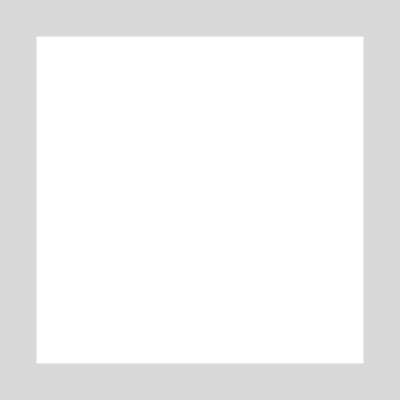
```mathematica
(*Show[{-Graphics-,VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle->Arrowheads[0]]}]*)
```

```mathematica
(*varreplace = Append[Wx[x,y,z]->Wz,varreplace]*)
```

```mathematica
varreplace2= varreplace
```

{Nx[x,y,z]→Nx,Ny[x,y,z]→Ny,Nz[x,y,z]→Nz,Nx^(1,0,0)[x,y,z]→dNxdx,Nx^(0,1,0)[x,y,z]→dNxdy,Nx^(0,0,1)[x,y,z]→dNxdz,Ny^(1,0,0)[x,y,z]→dNydx,Ny^(0,1,0)[x,y,z]→dNydy,Ny^(0,0,1)[x,y,z]→dNydz,Nz^(1,0,0)[x,y,z]→dNzdx,Nz^(0,1,0)[x,y,z]→dNzdy,Nz^(0,0,1)[x,y,z]→dNzdz,Nx^(2,0,0)[x,y,z]→d2Nxdxdx,Nx^(1,1,0)[x,y,z]→d2Nxdxdy,Nx^(1,0,1)[x,y,z]→d2Nxdxdz,Nx^(1,1,0)[x,y,z]→d2Nxdydx,Nx^(0,2,0)[x,y,z]→d2Nxdydy,Nx^(0,1,1)[x,y,z]→d2Nxdydz,Nx^(1,0,1)[x,y,z]→d2Nxdzdx,Nx^(0,1,1)[x,y,z]→d2Nxdzdy,Nx^(0,0,2)[x,y,z]→d2Nxdzdz,Ny^(2,0,0)[x,y,z]→d2Nydxdx,Ny^(1,1,0)[x,y,z]→d2Nydxdy,Ny^(1,0,1)[x,y,z]→d2Nydxdz,Ny^(1,1,0)[x,y,z]→d2Nydydx,Ny^(0,2,0)[x,y,z]→d2Nydydy,Ny^(0,1,1)[x,y,z]→d2Nydydz,Ny^(1,0,1)[x,y,z]→d2Nydzdx,Ny^(0,1,1)[x,y,z]→d2Nydzdy,Ny^(0,0,2)[x,y,z]→d2Nydzdz,Nz^(2,0,0)[x,y,z]→d2Nzdxdx,Nz^(1,1,0)[x,y,z]→d2Nzdxdy,Nz^(1,0,1)[x,y,z]→d2Nzdxdz,Nz^(1,1,0)[x,y,z]→d2Nzdydx,Nz^(0,2,0)[x,y,z]→d2Nzdydy,Nz^(0,1,1)[x,y,z]→d2Nzdydz,Nz^(1,0,1)[x,y,z]→d2Nzdzdx,Nz^(0,1,1)[x,y,z]→d2Nzdzdy,Nz^(0,0,2)[x,y,z]→d2Nzdzdz,Nx[x,y]→Nx,Ny[x,y]→Ny,Nx^(1,0)[x,y]→dNxdx,Nx^(0,1)[x,y]→dNxdy,Ny^(1,0)[x,y]→dNydx,Ny^(0,1)[x,y]→dNydy,Nx^(2,0)[x,y]→d2Nxdxdx,Nx^(1,1)[x,y]→d2Nxdxdy,Nx^(1,1)[x,y]→d2Nxdydx,Nx^(0,2)[x,y]→d2Nxdydy,Ny^(2,0)[x,y]→d2Nydxdx,Ny^(1,1)[x,y]→d2Nydxdy,Ny^(1,1)[x,y]→d2Nydydx,Ny^(0,2)[x,y]→d2Nydydy,θ[x,y,z]→θ,ϕ[x,y,z]→ϕ,θ^(1,0,0)[x,y,z]→dθdx,θ^(0,1,0)[x,y,z]→dθdy,θ^(0,0,1)[x,y,z]→dθdz,ϕ^(1,0,0)[x,y,z]→dϕdx,ϕ^(0,1,0)[x,y,z]→dϕdy,ϕ^(0,0,1)[x,y,z]→dϕdz,θ^(2,0,0)[x,y,z]→d2θdxdx,θ^(1,1,0)[x,y,z]→d2θdxdy,θ^(1,0,1)[x,y,z]→d2θdxdz,θ^(1,1,0)[x,y,z]→d2θdydx,θ^(0,2,0)[x,y,z]→d2θdydy,θ^(0,1,1)[x,y,z]→d2θdydz,θ^(1,0,1)[x,y,z]→d2θdzdx,θ^(0,1,1)[x,y,z]→d2θdzdy,θ^(0,0,2)[x,y,z]→d2θdzdz,ϕ^(2,0,0)[x,y,z]→d2ϕdxdx,ϕ^(1,1,0)[x,y,z]→d2ϕdxdy,ϕ^(1,0,1)[x,y,z]→d2ϕdxdz,ϕ^(1,1,0)[x,y,z]→d2ϕdydx,ϕ^(0,2,0)[x,y,z]→d2ϕdydy,ϕ^(0,1,1)[x,y,z]→d2ϕdydz,ϕ^(1,0,1)[x,y,z]→d2ϕdzdx,ϕ^(0,1,1)[x,y,z]→d2ϕdzdy,ϕ^(0,0,2)[x,y,z]→d2ϕdzdz,ϕ[x,y]→ϕ,ϕ^(1,0)[x,y]→dϕdx,ϕ^(0,1)[x,y]→dϕdy,ϕ^(2,0)[x,y]→d2ϕdxdx,ϕ^(1,1)[x,y]→d2ϕdxdy,ϕ^(1,1)[x,y]→d2ϕdydx,ϕ^(0,2)[x,y]→d2ϕdydy}

```mathematica
varreplace={Nx[x,y,z]->Nx,Ny[x,y,z]->Ny,Nz[x,y,z]->Nz,Derivative[1,0,0][Nx][x,y,z]->dNxdx,Derivative[0,1,0][Nx][x,y,z]->dNxdy,Derivative[0,0,1][Nx][x,y,z]->dNxdz,Derivative[1,0,0][Ny][x,y,z]->dNydx,Derivative[0,1,0][Ny][x,y,z]->dNydy,Derivative[0,0,1][Ny][x,y,z]->dNydz,Derivative[1,0,0][Nz][x,y,z]->dNzdx,Derivative[0,1,0][Nz][x,y,z]->dNzdy,Derivative[0,0,1][Nz][x,y,z]->dNzdz,Derivative[2,0,0][Nx][x,y,z]->d2Nxdxdx,Derivative[1,1,0][Nx][x,y,z]->d2Nxdxdy,Derivative[1,0,1][Nx][x,y,z]->d2Nxdxdz,Derivative[1,1,0][Nx][x,y,z]->d2Nxdydx,Derivative[0,2,0][Nx][x,y,z]->d2Nxdydy,Derivative[0,1,1][Nx][x,y,z]->d2Nxdydz,Derivative[1,0,1][Nx][x,y,z]->d2Nxdzdx,Derivative[0,1,1][Nx][x,y,z]->d2Nxdzdy,Derivative[0,0,2][Nx][x,y,z]->d2Nxdzdz,Derivative[2,0,0][Ny][x,y,z]->d2Nydxdx,Derivative[1,1,0][Ny][x,y,z]->d2Nydxdy,Derivative[1,0,1][Ny][x,y,z]->d2Nydxdz,Derivative[1,1,0][Ny][x,y,z]->d2Nydydx,Derivative[0,2,0][Ny][x,y,z]->d2Nydydy,Derivative[0,1,1][Ny][x,y,z]->d2Nydydz,Derivative[1,0,1][Ny][x,y,z]->d2Nydzdx,Derivative[0,1,1][Ny][x,y,z]->d2Nydzdy,Derivative[0,0,2][Ny][x,y,z]->d2Nydzdz,Derivative[2,0,0][Nz][x,y,z]->d2Nzdxdx,Derivative[1,1,0][Nz][x,y,z]->d2Nzdxdy,Derivative[1,0,1][Nz][x,y,z]->d2Nzdxdz,Derivative[1,1,0][Nz][x,y,z]->d2Nzdydx,Derivative[0,2,0][Nz][x,y,z]->d2Nzdydy,Derivative[0,1,1][Nz][x,y,z]->d2Nzdydz,Derivative[1,0,1][Nz][x,y,z]->d2Nzdzdx,Derivative[0,1,1][Nz][x,y,z]->d2Nzdzdy,Derivative[0,0,2][Nz][x,y,z]->d2Nzdzdz,Nx[x,y]->Nx,Ny[x,y]->Ny,Derivative[1,0][Nx][x,y]->dNxdx,Derivative[0,1][Nx][x,y]->dNxdy,Derivative[1,0][Ny][x,y]->dNydx,Derivative[0,1][Ny][x,y]->dNydy,Derivative[2,0][Nx][x,y]->d2Nxdxdx,Derivative[1,1][Nx][x,y]->d2Nxdxdy,Derivative[1,1][Nx][x,y]->d2Nxdydx,Derivative[0,2][Nx][x,y]->d2Nxdydy,Derivative[2,0][Ny][x,y]->d2Nydxdx,Derivative[1,1][Ny][x,y]->d2Nydxdy,Derivative[1,1][Ny][x,y]->d2Nydydx,Derivative[0,2][Ny][x,y]->d2Nydydy,θ[x,y,z]->θ,ϕ[x,y,z]->ϕ,Derivative[1,0,0][θ][x,y,z]->dθdx,Derivative[0,1,0][θ][x,y,z]->dθdy,Derivative[0,0,1][θ][x,y,z]->dθdz,Derivative[1,0,0][ϕ][x,y,z]->dϕdx,Derivative[0,1,0][ϕ][x,y,z]->dϕdy,Derivative[0,0,1][ϕ][x,y,z]->dϕdz,Derivative[2,0,0][θ][x,y,z]->d2θdxdx,Derivative[1,1,0][θ][x,y,z]->d2θdxdy,Derivative[1,0,1][θ][x,y,z]->d2θdxdz,Derivative[1,1,0][θ][x,y,z]->d2θdydx,Derivative[0,2,0][θ][x,y,z]->d2θdydy,Derivative[0,1,1][θ][x,y,z]->d2θdydz,Derivative[1,0,1][θ][x,y,z]->d2θdzdx,Derivative[0,1,1][θ][x,y,z]->d2θdzdy,Derivative[0,0,2][θ][x,y,z]->d2θdzdz,Derivative[2,0,0][ϕ][x,y,z]->d2ϕdxdx,Derivative[1,1,0][ϕ][x,y,z]->d2ϕdxdy,Derivative[1,0,1][ϕ][x,y,z]->d2ϕdxdz,Derivative[1,1,0][ϕ][x,y,z]->d2ϕdydx,Derivative[0,2,0][ϕ][x,y,z]->d2ϕdydy,Derivative[0,1,1][ϕ][x,y,z]->d2ϕdydz,Derivative[1,0,1][ϕ][x,y,z]->d2ϕdzdx,Derivative[0,1,1][ϕ][x,y,z]->d2ϕdzdy,Derivative[0,0,2][ϕ][x,y,z]->d2ϕdzdz,ϕ[x,y]->ϕ,Derivative[1,0][ϕ][x,y]->dϕdx,Derivative[0,1][ϕ][x,y]->dϕdy,Derivative[2,0][ϕ][x,y]->d2ϕdxdx,Derivative[1,1][ϕ][x,y]->d2ϕdxdy,Derivative[1,1][ϕ][x,y]->d2ϕdydx,Derivative[0,2][ϕ][x,y]->d2ϕdydy}
```

{Nx[x,y,z]→Nx,Ny[x,y,z]→Ny,Nz[x,y,z]→Nz,Nx^(1,0,0)[x,y,z]→dNxdx,Nx^(0,1,0)[x,y,z]→dNxdy,Nx^(0,0,1)[x,y,z]→dNxdz,Ny^(1,0,0)[x,y,z]→dNydx,Ny^(0,1,0)[x,y,z]→dNydy,Ny^(0,0,1)[x,y,z]→dNydz,Nz^(1,0,0)[x,y,z]→dNzdx,Nz^(0,1,0)[x,y,z]→dNzdy,Nz^(0,0,1)[x,y,z]→dNzdz,Nx^(2,0,0)[x,y,z]→d2Nxdxdx,Nx^(1,1,0)[x,y,z]→d2Nxdxdy,Nx^(1,0,1)[x,y,z]→d2Nxdxdz,Nx^(1,1,0)[x,y,z]→d2Nxdydx,Nx^(0,2,0)[x,y,z]→d2Nxdydy,Nx^(0,1,1)[x,y,z]→d2Nxdydz,Nx^(1,0,1)[x,y,z]→d2Nxdzdx,Nx^(0,1,1)[x,y,z]→d2Nxdzdy,Nx^(0,0,2)[x,y,z]→d2Nxdzdz,Ny^(2,0,0)[x,y,z]→d2Nydxdx,Ny^(1,1,0)[x,y,z]→d2Nydxdy,Ny^(1,0,1)[x,y,z]→d2Nydxdz,Ny^(1,1,0)[x,y,z]→d2Nydydx,Ny^(0,2,0)[x,y,z]→d2Nydydy,Ny^(0,1,1)[x,y,z]→d2Nydydz,Ny^(1,0,1)[x,y,z]→d2Nydzdx,Ny^(0,1,1)[x,y,z]→d2Nydzdy,Ny^(0,0,2)[x,y,z]→d2Nydzdz,Nz^(2,0,0)[x,y,z]→d2Nzdxdx,Nz^(1,1,0)[x,y,z]→d2Nzdxdy,Nz^(1,0,1)[x,y,z]→d2Nzdxdz,Nz^(1,1,0)[x,y,z]→d2Nzdydx,Nz^(0,2,0)[x,y,z]→d2Nzdydy,Nz^(0,1,1)[x,y,z]→d2Nzdydz,Nz^(1,0,1)[x,y,z]→d2Nzdzdx,Nz^(0,1,1)[x,y,z]→d2Nzdzdy,Nz^(0,0,2)[x,y,z]→d2Nzdzdz,Nx[x,y]→Nx,Ny[x,y]→Ny,Nx^(1,0)[x,y]→dNxdx,Nx^(0,1)[x,y]→dNxdy,Ny^(1,0)[x,y]→dNydx,Ny^(0,1)[x,y]→dNydy,Nx^(2,0)[x,y]→d2Nxdxdx,Nx^(1,1)[x,y]→d2Nxdxdy,Nx^(1,1)[x,y]→d2Nxdydx,Nx^(0,2)[x,y]→d2Nxdydy,Ny^(2,0)[x,y]→d2Nydxdx,Ny^(1,1)[x,y]→d2Nydxdy,Ny^(1,1)[x,y]→d2Nydydx,Ny^(0,2)[x,y]→d2Nydydy,θ[x,y,z]→θ,ϕ[x,y,z]→ϕ,θ^(1,0,0)[x,y,z]→dθdx,θ^(0,1,0)[x,y,z]→dθdy,θ^(0,0,1)[x,y,z]→dθdz,ϕ^(1,0,0)[x,y,z]→dϕdx,ϕ^(0,1,0)[x,y,z]→dϕdy,ϕ^(0,0,1)[x,y,z]→dϕdz,θ^(2,0,0)[x,y,z]→d2θdxdx,θ^(1,1,0)[x,y,z]→d2θdxdy,θ^(1,0,1)[x,y,z]→d2θdxdz,θ^(1,1,0)[x,y,z]→d2θdydx,θ^(0,2,0)[x,y,z]→d2θdydy,θ^(0,1,1)[x,y,z]→d2θdydz,θ^(1,0,1)[x,y,z]→d2θdzdx,θ^(0,1,1)[x,y,z]→d2θdzdy,θ^(0,0,2)[x,y,z]→d2θdzdz,ϕ^(2,0,0)[x,y,z]→d2ϕdxdx,ϕ^(1,1,0)[x,y,z]→d2ϕdxdy,ϕ^(1,0,1)[x,y,z]→d2ϕdxdz,ϕ^(1,1,0)[x,y,z]→d2ϕdydx,ϕ^(0,2,0)[x,y,z]→d2ϕdydy,ϕ^(0,1,1)[x,y,z]→d2ϕdydz,ϕ^(1,0,1)[x,y,z]→d2ϕdzdx,ϕ^(0,1,1)[x,y,z]→d2ϕdzdy,ϕ^(0,0,2)[x,y,z]→d2ϕdzdz,ϕ[x,y]→ϕ,ϕ^(1,0)[x,y]→dϕdx,ϕ^(0,1)[x,y]→dϕdy,ϕ^(2,0)[x,y]→d2ϕdxdx,ϕ^(1,1)[x,y]→d2ϕdxdy,ϕ^(1,1)[x,y]→d2ϕdydx,ϕ^(0,2)[x,y]→d2ϕdydy}